```mathematica
(*slo*)
sico={131,179,215,250,277,287,319,342,368,406,441,477,525,571,632,684,730,756,802,841,897,934,977,1009,1032,1067,1103,1136,1171,1199,1216,1223,1223+8,1223+8+28,1223+8+28+21};
dtests={1045,1197,916,590,871,1121,1026,1184,1200,872,731,1257,1240,1181,1075,1387,999,596,1125,1288,1095,1050,1188,655,489,1202,1212,1144,1234,1232,572,544,541,1168,1023,1193};
dcases={49,48,36,35,27,10,32,23,26,38,35,36,48,46,61,52,46,26,46,39,56,37,43,20,23,35,36,33,36,28,17,7,8,27,21,36};
Length[dcases]
Length[dtests]
adtests=dcases/dtests Mean[dtests]//N
cpert=Accumulate[N[adtests]]+131
timecpert=Table[i,{i,1,Length[cpert]}];
(*sico[[-34;;]]-cpert;*)
Mean[dtests]//N
cpstartdate={2020,3,12};
sico=Accumulate[dcases]+82
timesico=Table[i,{i,1,Length[sico]}];
```

36

36

{47.467,40.5937,39.7849,60.052,31.3803,9.03038,31.5729,19.6647,21.9333,44.1142,48.4688,28.992,39.186,39.4293,57.4425,37.9523,46.6127,44.161,41.392,30.6521,51.7709,35.6717,36.6407,30.9101,47.6136,29.4765,30.0685,29.2011,29.5324,23.0069,30.086,13.026,14.9694,23.4009,20.7805,30.5474}

{178.467,219.061,258.846,318.898,350.278,359.308,390.881,410.546,432.479,476.593,525.062,554.054,593.24,632.67,690.112,728.064,774.677,818.838,860.23,890.882,942.653,978.325,1014.97,1045.88,1093.49,1122.97,1153.03,1182.24,1211.77,1234.77,1264.86,1277.89,1292.86,1316.26,1337.04,1367.58}

1012.31

{131,179,215,250,277,287,319,342,368,406,441,477,525,571,632,684,730,756,802,841,897,934,977,997,1020,1055,1091,1124,1160,1188,1205,1212,1220,1247,1268,1304}

```mathematica
cp0={1420.4682436753844,156.7972712988734,0.12351920906743179};
```

```mathematica
cp0=cp0-PseudoInverse[dwf[cp0,timecpert,cpert]].wf[cp0,timecpert,cpert]
```

{1501.26,196.037,0.113339}

```mathematica
{cp20,ik,ie,il}=GNiteration[cpert,cp0]
```

{{1499.99,197.072,0.114401},5,7.35532×10^-9,36}

{1507.76,203.502,0.112326}

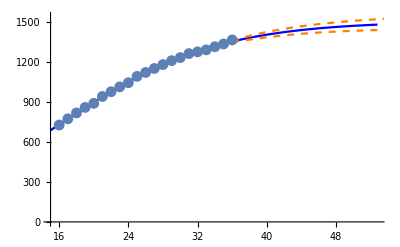
{-Graphics-,14.705,4.99353,30.5474,-19.4614,90.7028}

```mathematica
{cp20,abctab,winds}=stepGNiteration[cpert,cp0,21,timecpert,{1,0}];
cp20
cpert20=cpert[[-21;;]];
datastats[cpert20,cp20,1.8,2,timecpert[[-21;;]]]
```

```mathematica
sip0={1384.8615587986176,145.83741820834007,0.12921631186746152};
```

```mathematica
sip0=sip0-PseudoInverse[dwf[sip0,timesico,sico]].wf[sip0,timesico,sico]
```

{1384.86,145.837,0.129216}

```mathematica
{sip0,ik,ie,il}=GNiteration[sico,sip0]
```

{{1384.86,145.837,0.129216},1,2.51482×10^-11,36}

{1418.29,175.351,0.117727}

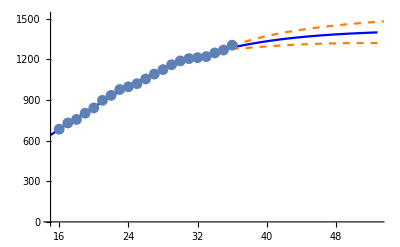
{-Graphics-,13.4011,9.56377,36,-19.3646,91.9418}

```mathematica
{sip20,abctab,winds}=stepGNiteration[sico,sip0,21,timesico,{1,0}];
sip20
sico21=sico[[-21;;]];
datastats[sico21,sip20,1.8,2,timesico[[-21;;]]]
```

```mathematica
(*italy*)
itco={3,3,9,76,124,229,322,400,650,888,1128,1679,2036,2502,3089,3858,4636,5883,7375,9172,10149,12462,15113,17660,21157,24747,27980,31506,35713,41035,47021,53578,59138,63928,69176,74386,80539,86498,92472,97689,101739,105792,110574,115242,119827,124632,128948,132547,135586,139422,143626,147577,152271,156363,159516,162488,165155,168941,172434};
timeitco=Table[i,{i,1,Length[itco]}];
itstartdate={2020,2,21};
```

```mathematica
ip0={174788.1382104429,823.1473098522238,0.13824837796814018};
```

```mathematica
ip0=ip0-PseudoInverse[dwf[ip0,timeitco,itco]].wf[ip0,timeitco,itco]
```

{174788.,823.147,0.138248}

```mathematica
{ip0,ik,ie,il}=GNiteration[itco,ip0]
```

{{174788.,823.147,0.138248},1,2.31476×10^-9,59}

{217340.,6718.05,0.0809455}

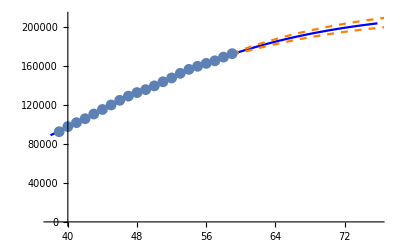
{-Graphics-,2840.71,574.625,3493,-16.4372,79.3384}

```mathematica
{itp20,abctab,winds}=stepGNiteration[itco,ip0,21,timeitco,{1,0}];
itp20
itco21=itco[[-21;;]];
datastats[itco21,itp20,1.8,2,timeitco[[-21;;]]]
```

```mathematica
avco={10,10,18,24,37,47,66,104,112,131,182,302,361,504,800,959,1132,1332,1646,1843,2649,3024,3631,4486,5282,5888,7029,7697,8291,8813,9618,10182,10711,11129,11525,11766,11983,12297,12640,12969,13248,13560,13807,13937,14043,14234,14370,14448,14553};
Length[avco]
timeavco=Table[i,{i,1,Length[avco]}];
avstartdate={2020,3,2};
```

49

```mathematica
avp0={14252.234732511146,36.9115421452583,0.2140};
```

```mathematica
avp0=avp0-PseudoInverse[dwf[avp0,timeavco,avco]].wf[avp0,timeavco,avco]
```

{14252.9,36.9485,0.214051}

```mathematica
{avp0,ik,ie,il}=GNiteration[avco,avp0]
```

{{14252.2,36.9115,0.214091},7,7.1463×10^-7,49}

{15155.3,279.435,0.145135}

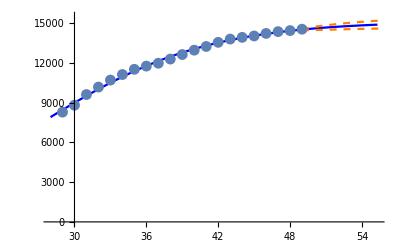
{-Graphics-,82.1101,118.543,105,-21.6136,96.0258}

```mathematica
{avp20,abctab,winds}=stepGNiteration[avco,avp0,21,timeavco,{1,0}];
avp20
avco21=avco[[-21;;]];
datastats[avco21,avp20,1.3,1,timeavco[[-21;;]]]
```

```mathematica
(*germany*)
gerco={7,8,10,12,12,12,13,14,14,14,14,16,16,16,16,16,16,16,16,16,16,16,16,16,16,18,21,26,57,129,157,196,262,534,639,795,1112,1139,1296,1567,2369,3062,3795,4838,6012,7156,8198,10999,18323,21463,24774,29212,31554,36508,42288,48582,52547,57298,61913,67366,73522,79696,85778,91714,95391,99765,103306,108202,113525,117658,120479,123016,125098,127584,130450,133830,135549,138498};
Length[gerco]
timegerco=Table[i,{i,1,Length[gerco]}];
Clear[lgerco,timelgerco];
lgerco=gerco[[34;;]];
Length[lgerco]
timelgerco=Table[i,{i,1,Length[lgerco]}];
gerstartdate={2020,3,6};
```

78

45

```mathematica
gp0={141217.4695898566,1261.0254956584702,0.1713149345909435};
```

```mathematica
{gp0,ik,ie,il}=GNiteration[lgerco,gp0]
```

{{141217.,1261.03,0.171315},1,1.16183×10^-8,45}

{147930.,2289.37,0.148031}

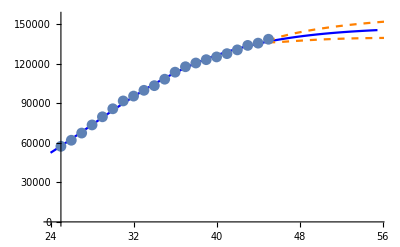
{-Graphics-,1431.44,922.005,2949,-16.946,93.6239}

```mathematica
{gp20,abctab,winds}=stepGNiteration[lgerco,gp0,21,timelgerco,{1,0}];
gp20
gerco21=lgerco[[-21;;]];
datastats[gerco21,gp20,1.5,2,timelgerco[[-21;;]]]
```

```mathematica
ameri={62,62,64,108,129,148,213,213,213,472,696,987,1264,1678,1678,1678,3503,3536,7087,10442,15219,15219,31573,42164,51914,63570,68334,85228,103321,122653,140640,163199,187302,213600,241703,273808,307318,333811,363321,395503,425889,461275,492881,524514,553822,578268,604070,632781,657720,689588};
Length[ameri]
ameri=ameri[[-30;;]]
timemeri=Table[n,{n,1,Length[ameri]}];
ameristartdate={2020,3,20};
```

50

{15219,15219,31573,42164,51914,63570,68334,85228,103321,122653,140640,163199,187302,213600,241703,273808,307318,333811,363321,395503,425889,461275,492881,524514,553822,578268,604070,632781,657720,689588}

```mathematica
ap0={791146.531329434,24326.958364655366,0.17300849545766925};
```

```mathematica
{ap0,ik,ie,il}=GNiteration[ameri,ap0]
```

{{791147.,24327.,0.173008},1,9.78597×10^-9,30}

{827200.,29249.8,0.160815}

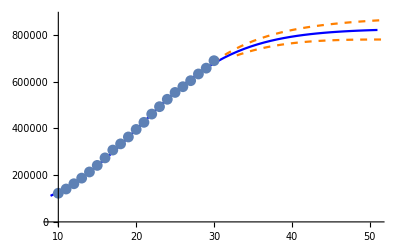
{-Graphics-,18611.8,4458.51,31868,-9.44111,83.3641}

```mathematica
{ap20,abctab,winds}=stepGNiteration[ameri,ap0,21,timemeri,{1,0}];
ap20
amer14=ameri[[-21;;]];
datastats[amer14,ap20,2,2,timemeri[[-21;;]]]
```

```mathematica
SetDirectory["/Users/peterkink/githubclone/pandemic-of-2020/docs"]
```

/Users/peterkink/githubclone/pandemic-of-2020/docs

{1490.42,196.357,0.115078}

{1507.76,203.502,0.112326}

{1507.76,203.502,0.112326}

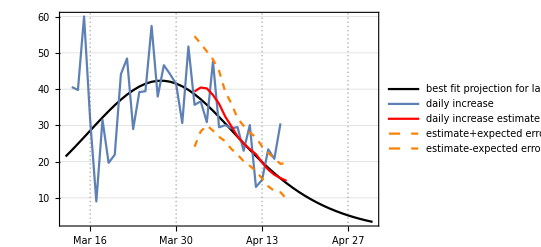
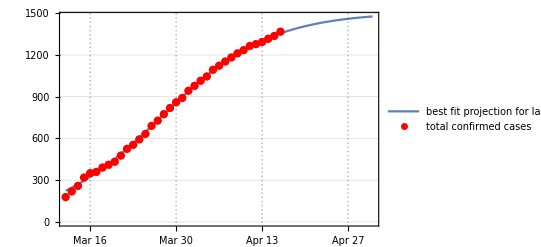
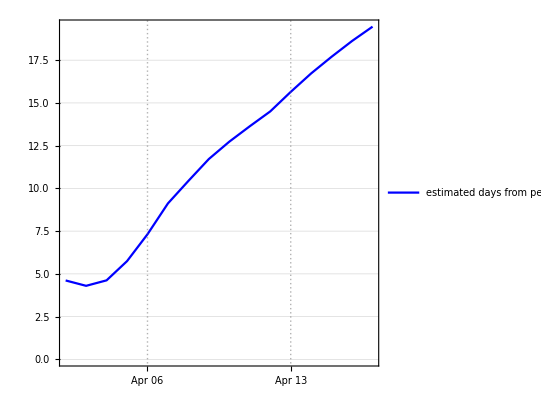
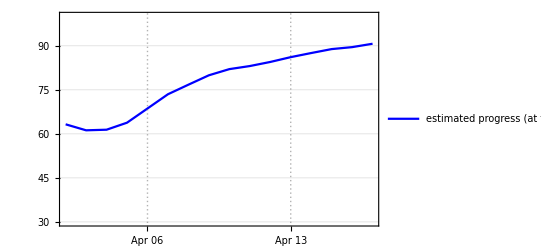

```mathematica
{graf,loggraf,dfpplot,progplot}=somegraphs[cp0,cp20,timecpert,cpert,cpstartdate,21,14,0]
```

```mathematica
Export["slograf.png",graf]
Export["slologgraf.png",loggraf]
Export["slodfgraf.png",dfpplot]
Export["sloprogplot.png",progplot]
```

slograf.png

slologgraf.png

slodfgraf.png

sloprogplot.png

{23056.4,55.8783,0.276821}

{217340.,6718.05,0.0809455}

{217340.,6718.05,0.0809455}

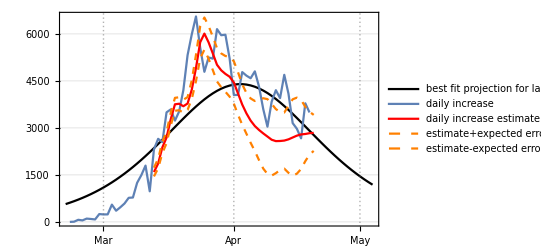
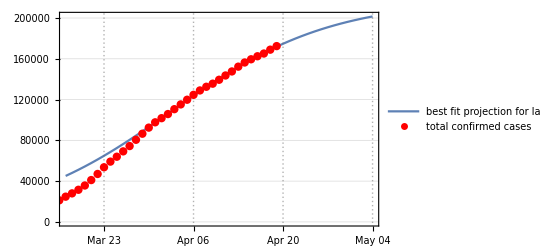
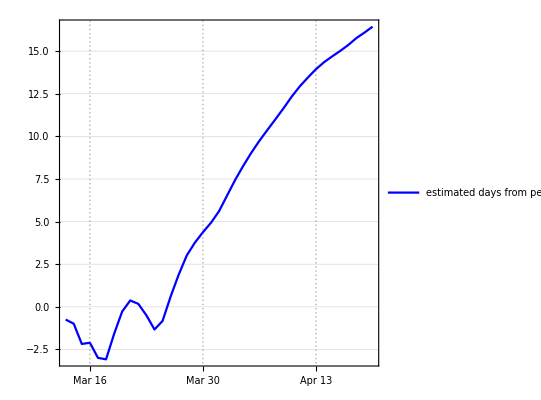
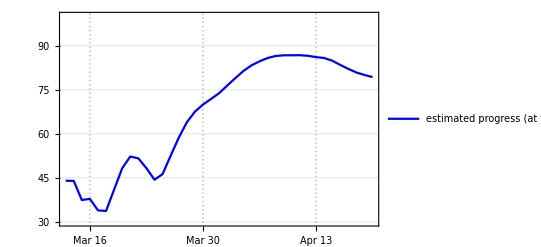

```mathematica
{graf,loggraf,dfpplot,progplot}=somegraphs[ip0,itp20,timeitco,itco,itstartdate,21,14,25]
```

```mathematica
Export["italygraf.png",graf]
Export["italyloggraf.png",loggraf]
Export["italydfgraf.png",dfpplot]
Export["italyprogplot.png",progplot]
```

italygraf.png

italyloggraf.png

italydfgraf.png

italyprogplot.png

{9943.54,14.6999,0.258747}

{15155.3,279.435,0.145135}

{15155.3,279.435,0.145135}

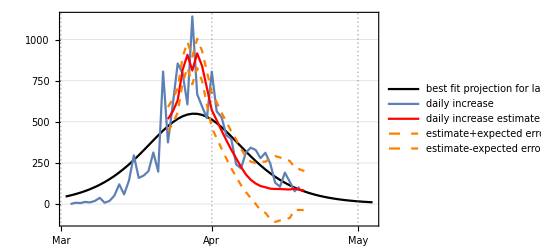
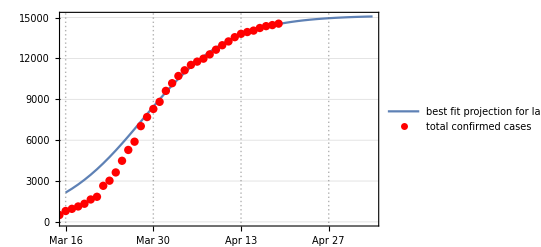
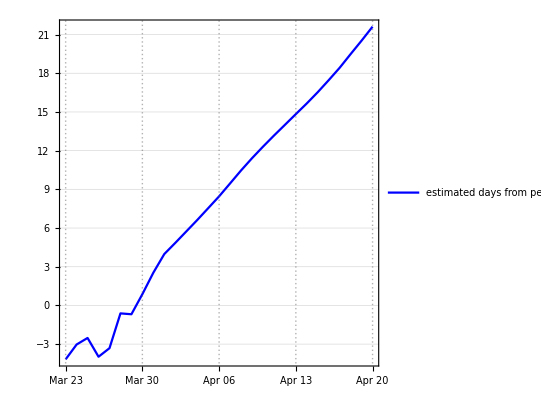
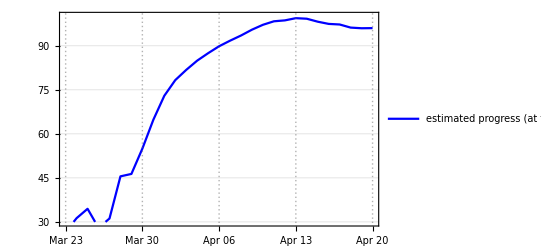

```mathematica
{graf,loggraf,dfpplot,progplot}=somegraphs[avp0,avp20,timeavco,avco,avstartdate,21,14,14]
```

```mathematica
Export["austriagraf.png",graf]
Export["austrialoggraf.png",loggraf]
Export["austriadfgraf.png",dfpplot]
Export["austriaprogplot.png",progplot]
```

austriagraf.png

austrialoggraf.png

austriadfgraf.png

austriaprogplot.png

{51026.4,128.882,0.327775}

{147930.,2289.37,0.148031}

{147930.,2289.37,0.148031}

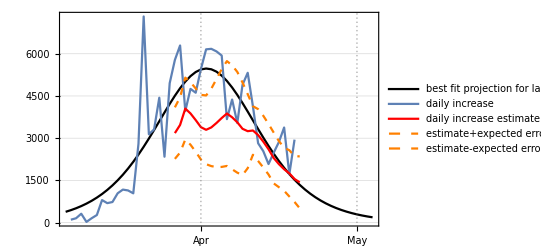
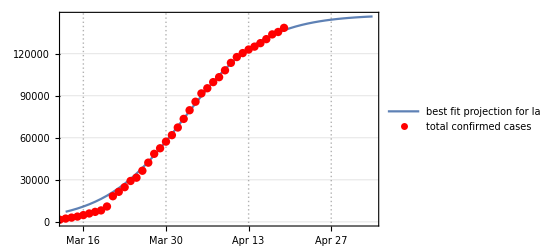
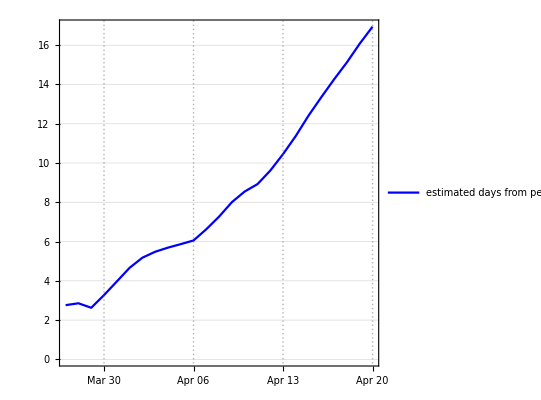
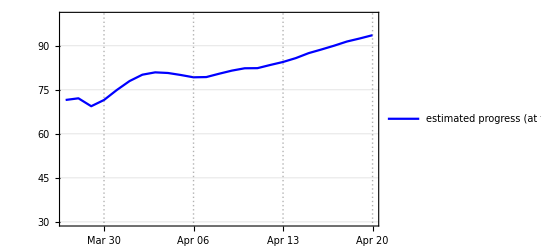

```mathematica
{graf,loggraf,dfpplot,progplot}=somegraphs[gp0,gp20,timelgerco,lgerco,gerstartdate,21,14,7]
```

{609519.,18667.,0.203405}

{827200.,29249.8,0.160815}

{827200.,29249.8,0.160815}

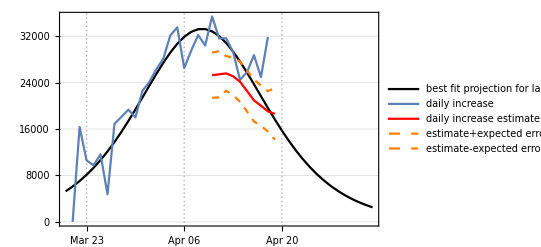
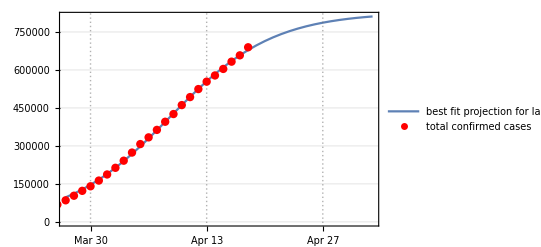
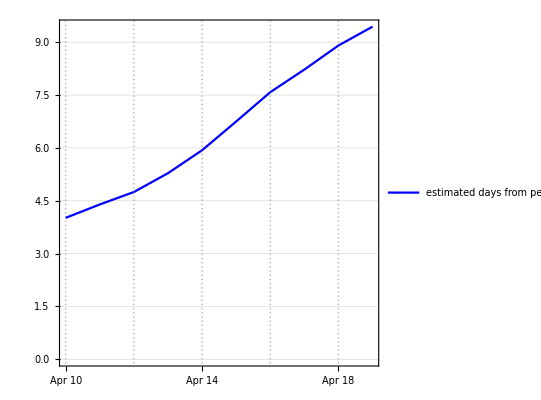
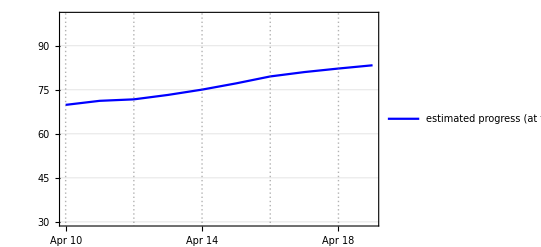

```mathematica
{graf,loggraf,dfpplot,progplot}=somegraphs[ap0,ap20,timemeri,ameri,ameristartdate,21,14,7]
```